# Hochschild Algebra in Book Notation

## The infix operators ⊗ and ⊕

© Computational Classnotes · CC BY-NC-SA 4.0

```mathematica
DateString[]
```

Wed 18 Nov 2026 01:37:47

Products and sums are written as in the books: a⊗b for the product and a⊕b for the sum. Type the symbols with Esc c* Esc and Esc c+ Esc. Scalars multiply by juxtaposition, as in q x⊗y, and -a is the additive inverse. Keep this notebook next to HochschildKit.wl.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["HochschildKit.wl"];
```

## 0. Intuition: what is a cochain?

### Cochains in geometry

Draw a shape out of points, edges and triangles. A 0-cochain puts a number on every point, like a temperature. A 1-cochain puts a number on every edge, like the work done walking along it. A 2-cochain puts a number on every triangle, like the flux through it.

In two dimensions: a square cut into two triangles. Red numbers sit on the points (a 0-cochain f), blue numbers on the oriented edges, green numbers inside the triangles. The middle panel shows the coboundary of f: each edge carries the change of f along it, and around every triangle these changes add up to 0. The right panel shows a 1-cochain ω that is not a gradient; its coboundary is the circulation around each triangle, a 2-cochain.

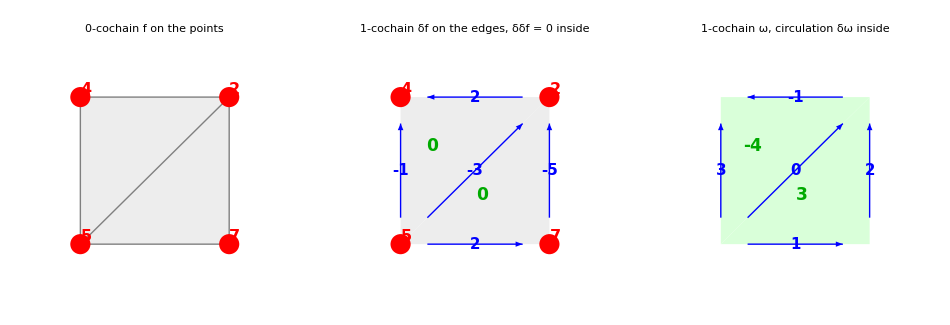

```mathematica
(* a square cut into two triangles: 4 points, 5 oriented edges, 2 triangles *)
pts = {{0, 0}, {1, 0}, {1, 1}, {0, 1}};
edg = {{1, 2}, {2, 3}, {3, 4}, {1, 4}, {1, 3}};             (* each edge points from its first vertex to its second *)
tri = {{1, 2, 3}, {1, 3, 4}};
fv = {5, 7, 2, 4};                                          (* 0-cochain: a number on each point *)
dfv = fv[[#[[2]]]] - fv[[#[[1]]]] & /@ edg;                 (* its coboundary: the change of fv along each edge *)
wv = {1, 2, -1, 3, 0};                                      (* a 1-cochain that is not a gradient *)
onEdge[c_, {i_, j_}] := c[[First@FirstPosition[edg, {i, j}]]];
dTri[c_] := onEdge[c, {#[[1]], #[[2]]}] + onEdge[c, {#[[2]], #[[3]]}] - onEdge[c, {#[[1]], #[[3]]}] & /@ tri;   (* circulation around each triangle *)
shrink[{a_, b_}] := {a + 0.18 (b - a), b - 0.18 (b - a)};
faces[col_] := {col, EdgeForm[], Polygon[pts[[#]]] & /@ tri};
edgeArrows[vals_, col_] := {col, Thick, Arrowheads[0.07], Arrow[shrink[pts[[#]]]] & /@ edg,
   MapThread[Text[Style[#1, 15, Bold, col, Background -> White], Mean[pts[[#2]]]] &, {vals, edg}]};
pointLabels := {Red, PointSize[0.05], Point[pts], MapThread[Text[Style[#1, 16, Bold, Red], #2, {-1.6, -1.6}] &, {fv, pts}]};
faceLabels[vals_] := MapThread[Text[Style[#1, 17, Bold, Darker[Green]], Mean[pts[[#2]]] + {0.12 Sign[#2[[2]] - #2[[3]] + 0.5], 0}] &, {vals, tri}];
opts = Sequence[PlotRange -> {{-0.35, 1.35}, {-0.35, 1.35}}, ImageSize -> 290];
GraphicsRow[{
  Graphics[{faces[GrayLevel[0.93]], Gray, Line[pts[[#]]] & /@ edg, pointLabels}, PlotLabel -> Style["0-cochain f on the points", 13], opts],
  Graphics[{faces[GrayLevel[0.93]], edgeArrows[dfv, Blue], faceLabels[dTri[dfv]], pointLabels}, PlotLabel -> Style["1-cochain δf on the edges, δδf = 0 inside", 13], opts],
  Graphics[{faces[Lighter[Green, 0.85]], edgeArrows[wv, Blue], faceLabels[dTri[wv]]}, PlotLabel -> Style["1-cochain ω, circulation δω inside", 13], opts]},
 Spacings -> 10, ImageSize -> 950]
```

In three dimensions: the surface of a tetrahedron, with a temperature on each vertex (red), the change of temperature along each edge (blue arrows) and a flux through each face (green, shaded by value).

```mathematica
(* a tetrahedron: 4 vertices, 6 edges, 4 triangular faces, all oriented by increasing vertex number *)
tv = {{0, 0, 0}, {1, 0, 0}, {1/2, Sqrt[3]/2, 0}, {1/2, Sqrt[3]/6, Sqrt[2/3]}};
te = Subsets[Range[4], {2}];
tf = Subsets[Range[4], {3}];
f3 = {3, 1, 4, 2};                                          (* 0-cochain: a temperature at each vertex *)
e3 = f3[[#[[2]]]] - f3[[#[[1]]]] & /@ te;                   (* 1-cochain: the change of temperature along each edge *)
g3 = {2, -1, 3, 1};                                         (* 2-cochain: a flux through each face *)
ctr = Mean[tv];
out[p_, s_] := p + s (p - ctr);                             (* push a label slightly outwards *)
Graphics3D[{
  MapThread[{Opacity[0.35], ColorData["TemperatureMap"][(#1 + 1)/4], EdgeForm[], Polygon[tv[[#2]]]} &, {g3, tf}],
  MapThread[Text[Style[Row[{"flux ", #1}], 14, Bold, Darker[Green]], out[Mean[tv[[#2]]], 0.05]] &, {g3, tf}],
  {Blue, Arrowheads[0.04], Arrow[Tube[{tv[[#[[1]]]] + 0.12 (tv[[#[[2]]]] - tv[[#[[1]]]]), tv[[#[[2]]]] - 0.12 (tv[[#[[2]]]] - tv[[#[[1]]]])}, 0.008]] & /@ te},
  MapThread[Text[Style[#1, 14, Bold, Blue, Background -> White], out[Mean[tv[[#2]]], 0.08]] &, {e3, te}],
  {Red, Sphere[tv, 0.035]},
  MapThread[Text[Style[#1, 16, Bold, Red], out[#2, 0.22]] &, {f3, tv}]},
 Boxed -> False, Lighting -> "Neutral", ViewPoint -> {2.2, -1.6, 1.3}, ViewVertical -> {0, 0, 1}, ImageSize -> 520,
 PlotLabel -> Style["red: 0-cochain on vertices   blue: 1-cochain on edges   green: 2-cochain on faces", 13]]
```

-Graphics3D-

The coboundary δ turns a p-cochain into a (p+1)-cochain by adding up its values around the boundary, with signs. On points it is a discrete gradient: (δf)(i→j)=f(j)-f(i). On edges it is a discrete curl. The rule δ^2=0 says the curl of a gradient vanishes.

```mathematica
(* a circle drawn as a triangle: vertices 1, 2, 3 and edges 1->2, 2->3, 3->1 *)
edges = {{1, 2}, {2, 3}, {3, 1}};
d0 = Table[Which[v == e[[2]], 1, v == e[[1]], -1, True, 0], {e, edges}, {v, 3}];   (* (δf)(i->j) = f(j) - f(i) *)
f0 = {5, 7, 2};       (* a 0-cochain: a number on each vertex *)
d0 . f0              (* its coboundary: the change of f along each edge *)
```

```mathematica
Total[d0 . f0]       (* going once around the loop, the changes always add up to 0 *)
```

A cochain with δω=0 is closed (a cocycle). If it is ω=δf it is exact (a coboundary). Every exact cochain is closed. A closed cochain that is not exact detects a hole: here, the one-unit circulation around the triangle.

```mathematica
ω = {1, 0, 0};      (* a 1-cochain: 1 on the first edge, 0 elsewhere; it goes once around *)
Quiet@Check[LinearSolve[d0, ω], "no solution: ω is not the coboundary of any 0-cochain"]
```

```mathematica
(* the hole is counted by the cohomology: dim H^1 = dim(1-cochains) - rank(d0) *)
3 - MatrixRank[d0]
```

Fill the triangle in and the circulation becomes the flux through the face, so it is no longer closed and the hole disappears:

```mathematica
(* fill the triangle in: one face, whose coboundary adds the three edge values *)
d1 = {{1, 1, 1}};
{d1 . d0, (3 - MatrixRank[d1]) - MatrixRank[d0]}     (* δδ = 0, and the hole is gone: H^1 = 0 *)
```

So cohomology = closed modulo exact = the holes and twists that cannot be removed by changing coordinates. This is the one idea to keep in mind for everything below.

### From geometry to algebra

Hochschild cohomology runs the same machine on an algebra A. A simplex with p+1 corners becomes a string of p elements (a_1,…,a_p), and taking a face becomes multiplying two neighbours, a_i⊗a_(i+1). A p-cochain assigns an element of A to every such string, and δ is the alternating sum over the faces. In low degrees each formula measures a familiar failure:

(δa)(x)=x⊗a⊕-(a⊗x)

how far a is from commuting with x (zero exactly for central elements);

δ(𝒟)(a,b)==a⊗𝒟(b)⊕-𝒟(a⊗b)⊕𝒟(a)⊗b

how far a linear map is from the Leibniz rule (zero exactly for derivations);

δ(ϕ)(a,b,c)==a⊗ϕ(b,c)⊕-ϕ(a⊗b,c)⊕ϕ(a,b⊗c)⊕-(ϕ(a,b)⊗c)

how far the bent product a⊗b⊕t ϕ(a,b) is from associative, to first order in t.

Geometry | Algebra (Hochschild)
a point | an element a of A
a p-simplex | a string (a1, ..., ap) of p elements
taking a face | multiplying neighbours, a_i⊗a_(i+1)
p-cochain: a number on each p-simplex | p-cochain: an element f(a1, ..., ap) of A
gradient, curl, divergence | the Hochschild differential δ
curl of a gradient is 0 | δ^2==0, which comes from associativity
closed but not exact: a hole | cocycle but not coboundary: a nonzero class in HH
a vector field | a derivation, a class in HH^1
a Poisson bivector, to be quantized | a bend of the product, a class in HH^2

For the functions on a smooth space this dictionary is a theorem (Hochschild-Kostant-Rosenberg): HH^1 is exactly the vector fields and HH^2 the bivector fields. For a finite-dimensional algebra it is the guiding picture, and section 7 shows each line of the table in action.

## 1. The two operators

An element of an algebra A is stored by its coefficients in the basis of A, and a Hochschild cochain by its array of values. a⊗b is the product of A on elements and the cup product on cochains; a⊕b is the sum. A cochain is applied to elements as in the books, f[a, b], and δ is the Hochschild differential.

```mathematica
ClearAll[Elt, Coch, δ, Generators];
zeroQ[w_] := AllTrue[Flatten[{Simplify[w]}], # === 0 &];
(* algebra elements: Elt[A, coefficients in the basis of A] *)
Generators[A_] := Elt[A, #] & /@ IdentityMatrix[AlgebraDimension[A]];
Elt /: CircleTimes[Elt[A_, u_], Elt[A_, v_]] := Elt[A, Expand[v . (u . Mu[A])]];
Elt /: CircleTimes[a_Elt, b_Elt, c__Elt] := CircleTimes[CircleTimes[a, b], c];
Elt /: CirclePlus[Elt[A_, u_], Elt[A_, v_]] := Elt[A, u + v];
Elt /: CirclePlus[a_Elt, b_Elt, c__Elt] := CirclePlus[CirclePlus[a, b], c];
Elt /: Times[c_, Elt[A_, u_]] /; FreeQ[c, Elt | Coch] := Elt[A, c u];
Elt /: Equal[Elt[A_, u_], Elt[A_, v_]] := zeroQ[u - v];
Elt /: Equal[Elt[_, u_], 0] := zeroQ[u];
Elt /: MakeBoxes[Elt[A_, u_], fmt_] := ToBoxes[With[{t = Total[MapThread[If[#2 == "1", #1, #1 Style[#2, Italic, ShowStringCharacters -> False]] &, {Simplify[u], A["Basis"]}]]}, t], fmt];
(* Hochschild cochains: Coch[A, array of values]; f[a, b] evaluates, f ⊗ g is the cup product *)
Coch /: CirclePlus[Coch[A_, f_], Coch[A_, g_]] := Coch[A, f + g];
Coch /: CircleTimes[Coch[A_, f_], Coch[A_, g_]] := Coch[A, Cup[A, f, g]];
Coch /: CirclePlus[a_Coch, b_Coch, c__Coch] := CirclePlus[CirclePlus[a, b], c];
Coch /: CircleTimes[a_Coch, b_Coch, c__Coch] := CircleTimes[CircleTimes[a, b], c];
Coch /: Times[c_, Coch[A_, f_]] /; FreeQ[c, Elt | Coch] := Coch[A, c f];
Coch /: Equal[Coch[A_, f_], Coch[A_, g_]] := zeroQ[f - g];
Coch /: Equal[Coch[_, f_], 0] := zeroQ[f];
Coch[A_, f_][a___Elt] := Elt[A, EvaluateCochain[f, {a}[[All, 2]]]];
δ[Coch[A_, f_]] := Coch[A, HDelta[A, f]];
Coch /: MakeBoxes[Coch[A_, f_], fmt_] := ToBoxes[Row[{"cochain in ", Superscript["C", CochainDegree[f]]}], fmt];
```

### How the books write it

A Coch object is a Hochschild cochain. In the books the space of n-cochains of A with values in a bimodule M is

C^n(A,M)=Hom_k(A^(⊗n),M)

the k-linear maps of n arguments f(a_1,…,a_n) from A to M. Here M = A, so a Coch is an element of C^n(A,A). The dictionary:

"In this notebook" | "In the books"
"Coch[A, f]  (p arguments)" | f∈C^p(A,A)=Hom_k(A^(⊗p),A)
all the cochains together | the Hochschild complex (C^•(A,A),δ)
"Coch[A, u]  (no arguments)" | C^0(A,A)=A
"δ[f]" | δf∈C^(p+1)(A,A), also written d or b
"CocycleQ[A, f]" | f∈Z^p(A,A)=ker δ, a cocycle
"CoboundaryQ[A, f]" | f∈B^p(A,A)=im δ, a coboundary
"a class from HHBasis" | [f]∈HH^p(A,A)=Z^p/B^p
"deg[f]" | |f|=p
"f[a1, ..., ap]" | f(a_1,…,a_p)
"f ⊗ g  (on cochains)" | the cup product f⌣g, also written f∪g or f·g
"f ∘ g,  Bracket[f, g]" | Gerstenhaber's f∘g and [f,g]
"CochainForm[A, f]" | the values f(e_i_1,…,e_i_p) on basis elements

Variants you will meet in other books:

Bar resolution: C^n(A,M)≅Hom_(A^e)(A^(⊗(n+2)),M) with A^e=A⊗A^op, which is how HH^n(A,M)=Ext_(A^e)^n(A,M) is usually defined.

Normalized cochains (C̄)^n: the cochains that vanish when any argument is 1. They have the same cohomology.

Shifted grading for the bracket: Gerstenhaber puts a p-cochain in degree p - 1, so that C^(•+1)(A,A) becomes a graded Lie algebra.

This notebook writes the cup product as ⊗ so that one operator covers all multiplication. The books write f⌣g.

## 2. Expanding, distributing and simplifying

BookExpand applies the ring axioms symbolically: it distributes ⊗ over ⊕, flattens nested products and sums, pulls scalars out, collects like terms and simplifies their coefficients. Declare which symbols are algebra elements; every other symbol is a scalar.

```mathematica
$Elements = {};
DeclareElements[s__Symbol] := ($Elements = Union[$Elements, {s}]);
scalarQ[s_] := FreeQ[s, CircleTimes | CirclePlus | _Elt | _Coch] && FreeQ[s, Alternatives @@ $Elements];
bookRules = {
  CirclePlus[p___, CirclePlus[r__], s___] :> CirclePlus[p, r, s],
  CircleTimes[p___, CircleTimes[r__], s___] :> CircleTimes[p, r, s],
  CircleTimes[p___, CirclePlus[r__], s___] :> (CirclePlus @@ (CircleTimes[p, #, s] & /@ {r})),
  CircleTimes[p___, Times[c_?scalarQ, e_], s___] :> c CircleTimes[p, e, s],
  Times[c_?scalarQ, CirclePlus[r__]] :> (CirclePlus @@ (c # & /@ {r})),
  CirclePlus[e_] :> e, CircleTimes[e_] :> e};
splitTerm[t_] := Module[{fs = If[Head[t] === Times, List @@ t, {t}]},
  {Times @@ Select[fs, scalarQ], Times @@ Select[fs, ! scalarQ[#] &]}];
collectTerms[e_] := Module[{ts = If[Head[e] === CirclePlus, List @@ e, {e}], g},
  g = Select[Normal@GroupBy[splitTerm /@ ts, Last -> First, Simplify@*Total], #[[2]] =!= 0 &];
  Which[g === {}, 0, Length[g] == 1, g[[1, 2]] g[[1, 1]], True, CirclePlus @@ (#[[2]] #[[1]] & /@ SortBy[g, First])]];
BookExpand[e_] := collectTerms[FixedPoint[ReplaceRepeated[#, bookRules] &, e]];
```

```mathematica
DeclareElements[a, b, c];
BookExpand[(a ⊕ b) ⊗ (a ⊕ b)]
```

```mathematica
BookExpand[(2 a ⊕ -b) ⊗ (a ⊕ 3 b)]
```

```mathematica
BookExpand[(a ⊕ b) ⊗ c ⊕ -(a ⊗ c)]          (* the a ⊗ c terms cancel *)
```

```mathematica
BookExpand[q (a ⊕ b) ⊗ (a ⊕ -b) ⊕ q b ⊗ b]
```

```mathematica
BookExpand[(a ⊕ b) ⊗ (b ⊕ c) ⊗ a]
```

## 3. Elements of an algebra

Dual numbers k[x]/(x^2): x⊗x==0 and (1⊕x)⊗(1⊕-x)==1.

```mathematica
A = DualNumbers[];
{one, x} = Generators[A];
x ⊗ x == 0
```

```mathematica
(one ⊕ x) ⊗ (one ⊕ -x)          (* (1 + x)(1 - x) = 1 - x^2 = 1 *)
```

The quantum plane k⟨x,y⟩/(x^2,y^2,yx-qxy) with a symbolic parameter q:

```mathematica
A = QuantumPlane[q];
{one, x, y, xy} = Generators[A];
y ⊗ x == q (x ⊗ y)
```

```mathematica
(x ⊕ y) ⊗ (x ⊕ y)
```

```mathematica
BookExpand[(a ⊕ b) ⊗ (a ⊕ b)] /. {a -> x, b -> y}
```

```mathematica
(x ⊕ y) ⊗ (x ⊕ y) /. q -> -1      (* exterior algebra: (x + y)^2 = 0 *)
```

The ring axioms, checked on every triple of basis elements:

```mathematica
gens = Generators[A];
And @@ Flatten@Table[(a ⊗ b) ⊗ c == a ⊗ (b ⊗ c), {a, gens}, {b, gens}, {c, gens}]
```

```mathematica
And @@ Flatten@Table[a ⊗ (b ⊕ c) == a ⊗ b ⊕ a ⊗ c, {a, gens}, {b, gens}, {c, gens}]
```

```mathematica
And @@ Table[one ⊗ a == a && a ⊗ one == a, {a, gens}]
```

## 4. Cochains and the Hochschild differential

On k[x]/(x^3) a 1-cocycle is a derivation, 𝒟(a⊗b)==𝒟(a)⊗b⊕a⊗𝒟(b):

```mathematica
B = TruncatedPolynomial[3];
{one, x, x2} = gens = Generators[B];
der = Coch[B, First@HHBasis[B, 1]];
der[x]
```

```mathematica
And @@ Flatten@Table[der[a ⊗ b] == der[a] ⊗ b ⊕ a ⊗ der[b], {a, gens}, {b, gens}]
```

The differential of a 2-cochain, exactly as written in the books:

δ(ϕ)(a,b,c)==a⊗ϕ(b,c)⊕-ϕ(a⊗b,c)⊕ϕ(a,b⊗c)⊕-(ϕ(a,b)⊗c)

```mathematica
SeedRandom[1]; ϕ = Coch[B, RandomCochain[B, 2]];
And @@ Flatten@Table[δ[ϕ][a, b, c] == a ⊗ ϕ[b, c] ⊕ -ϕ[a ⊗ b, c] ⊕ ϕ[a, b ⊗ c] ⊕ -(ϕ[a, b] ⊗ c),
  {a, gens}, {b, gens}, {c, gens}]
```

```mathematica
δ[δ[ϕ]] == 0
```

The cup product f⊗g evaluates as (f⊗g)(a,b,c)==f(a)⊗g(b,c), and δ is a graded derivation of it:

```mathematica
f = Coch[B, RandomCochain[B, 1]]; g = Coch[B, RandomCochain[B, 2]];
And @@ Flatten@Table[(f ⊗ g)[a, b, c] == f[a] ⊗ g[b, c], {a, gens}, {b, gens}, {c, gens}]
```

```mathematica
δ[f ⊗ g] == δ[f] ⊗ g ⊕ (-1)^1 f ⊗ δ[g]
```

## 5. Deformations in book notation

The class in HH^2 of the dual numbers deforms the product to x⊗x==-t, which stays associative for every t:

```mathematica
D0 = DualNumbers[];
At = HochschildAlgebra["k[x]/(x^2 + t)", {"1", "x"}, DeformedStructureConstants[D0, {First@HHBasis[D0, 2]}, t]];
{one, x} = gens = Generators[At];
x ⊗ x
```

```mathematica
(one ⊕ x) ⊗ (one ⊕ -x)
```

```mathematica
And @@ Flatten@Table[(a ⊗ b) ⊗ c == a ⊗ (b ⊗ c), {a, gens}, {b, gens}, {c, gens}]
```

The quantum plane at q = 1 - t: the commutator measures the first-order term.

```mathematica
Qt = QuantumPlane[1 - t];
{one, x, y, xy} = Generators[Qt];
y ⊗ x ⊕ -(x ⊗ y)
```

## 6. The Jacobi identity for the Gerstenhaber bracket

The composition f∘g (Esc sc Esc) inserts g into f with the Koszul signs, and the Gerstenhaber bracket is written exactly as in the books, with |f| = p, |g| = q:

[f,g]=f∘g⊕-(-1)^((p-1)(q-1))g∘f

```mathematica
deg[Coch[_, f_]] := CochainDegree[f];
Coch /: SmallCircle[Coch[A_, f_], Coch[A_, g_]] := Coch[A, GCircle[f, g]];
Bracket[f_Coch, g_Coch] := f ∘ g ⊕ -(-1)^((deg[f] - 1) (deg[g] - 1)) (g ∘ f);
```

The graded Jacobi identity, for f, g, h of degrees p, q, r:

(-1)^((p-1)(r-1))[f,[g,h]]⊕(-1)^((q-1)(p-1))[g,[h,f]]⊕(-1)^((r-1)(q-1))[h,[f,g]]=0

One instance on k[x]/(x^3), with random cochains of degrees 2, 1, 2:

```mathematica
jacobi[f_, g_, h_] := With[{p = deg[f], q = deg[g], r = deg[h]},
  (-1)^((p - 1) (r - 1)) Bracket[f, Bracket[g, h]] ⊕ (-1)^((q - 1) (p - 1)) Bracket[g, Bracket[h, f]] ⊕ (-1)^((r - 1) (q - 1)) Bracket[h, Bracket[f, g]]];
SeedRandom[7];
{f, g, h} = {Coch[B, RandomCochain[B, 2]], Coch[B, RandomCochain[B, 1]], Coch[B, RandomCochain[B, 2]]};
jacobi[f, g, h] == 0
```

Every combination of degrees p, q, r from 0 to 2, each with fresh random cochains:

```mathematica
Table[jacobi[Coch[B, RandomCochain[B, p]], Coch[B, RandomCochain[B, q]], Coch[B, RandomCochain[B, r]]] == 0,
  {p, 0, 2}, {q, 0, 2}, {r, 0, 2}] // Flatten // Counts
```

Graded antisymmetry, [f,g]=-(-1)^((p-1)(q-1))[g,f], and the differential as a bracket with the product, δf=(-1)^(p-1)[μ,f]:

```mathematica
Bracket[f, g] == -(-1)^((deg[f] - 1) (deg[g] - 1)) Bracket[g, f]
```

```mathematica
μ = Coch[B, Mu[B]];
δ[f] == (-1)^(deg[f] - 1) Bracket[μ, f]
```

On cohomology classes the bracket of cocycles is again a cocycle, and the Jacobi identity holds in HH^*. Here on the cocycles representing HH^1 and HH^2 of k[x]/(x^3):

```mathematica
classes = Coch[B, #] & /@ Join[HHBasis[B, 1], HHBasis[B, 2]];
And @@ Flatten@Table[δ[Bracket[u, v]] == 0 && jacobi[u, v, w] == 0, {u, classes}, {v, classes}, {w, classes}]
```

## 7. Motivating examples for each degree

### HH^0: the elements that commute with everything

The coboundary of an element is its commutator with everything else. In the quantum plane, x and y do not commute unless q = 1, but xy commutes with every element:

```mathematica
A = QuantumPlane[q];
{one, x, y, xy} = Generators[A];
cx = Coch[A, x[[2]]];          (* the element x, viewed as a 0-cochain *)
δ[cx][y] == y ⊗ x ⊕ -(x ⊗ y)
```

```mathematica
δ[cx][y]                    (* (q - 1) xy : x commutes with y only when q = 1 *)
```

```mathematica
δ[Coch[A, xy[[2]]]] == 0     (* xy commutes with everything: it lies in HH^0, the centre *)
```

### HH^1: derivations are vector fields

On k[x]/(x^3) the map x d/dx (the Euler field: it scales x^n by n) satisfies the Leibniz rule, so it is a 1-cocycle. A map that is not a derivation has a nonzero coboundary, and the coboundary says exactly how badly Leibniz fails:

```mathematica
B = TruncatedPolynomial[3];
{one, x, x2} = gens = Generators[B];
eu = Coch[B, {{0, 0, 0}, {0, 1, 0}, {0, 0, 2}}];   (* x d/dx : 1 -> 0, x -> x, x^2 -> 2 x^2 *)
{eu[x], eu[x2], eu[x ⊗ x] == eu[x] ⊗ x ⊕ x ⊗ eu[x]}
```

```mathematica
δ[eu] == 0                   (* the Leibniz rule is exactly the cocycle condition *)
```

```mathematica
notDer = Coch[B, {{0, 0, 0}, {0, 1, 0}, {0, 0, 1}}];   (* x -> x, x^2 -> x^2 : not a derivation *)
δ[notDer][x, x]               (* x D(x) - D(x^2) + D(x) x : how far it is from Leibniz *)
```

```mathematica
HHDimension[B, 1]                  (* two independent vector fields: x d/dx and x^2 d/dx *)
```

### HH^2: bending the product

A 2-cocycle ϕ bends the multiplication to a⊗b⊕t ϕ(a,b). For the dual numbers k[x]/(x^2) the only bend is x^2=-t. Geometrically, k[x]/(x^2) is a double point: a point carrying one tangent direction. The bend pulls it apart into two separate points.

```mathematica
D0 = DualNumbers[];
{one, x} = Generators[D0];
ϕ = Coch[D0, First@HHBasis[D0, 2]];
star[a_, b_] := a ⊗ b ⊕ t ϕ[a, b];      (* the bent product *)
star[x, x]                          (* x x = -t instead of 0 *)
```

```mathematica
{δ[ϕ] == 0, star[star[x, x], x] == star[x, star[x, x]]}    (* the bend respects associativity *)
```

```mathematica
Solve[X^2 == -t, X] /. t -> -1      (* at t = -1 the double point x^2 = 0 splits into the two points x = 1, x = -1 *)
```

A coboundary only bends the product by a change of coordinates, which is why HH^2 counts the genuinely different deformations:

```mathematica
g = Coch[D0, {{0, 0}, {1, 0}}];      (* g(1) = 0, g(x) = 1 *)
{CoboundaryQ[D0, δ[g][[2]]], CoboundaryQ[D0, ϕ[[2]]]}   (* a coboundary only changes coordinates; ϕ is a genuine bend *)
```

One step further, HH^3 holds the obstructions: a bend that works to first order may fail to extend to all orders, and the failure is a class in HH^3, as in section 5.

© Computational Classnotes · CC BY-NC-SA 4.0